# Searching for rules that generate elementary particle behavior in the Wolfram Model

Paul Fischer
Department of Physics & Astronomy, California State University, Long Beach
(Dated: January 15, 2021)

Topological obstructions in a hypergraph that are locally stable under the application of rules are candidates for elementary particles in the Wolfram Model. In this project notebook, we create a hypergraph from a planar, triangular tiling, insert a nonplanar hypergraph (K_5 or K_(3,3)) as an obstruction, and search for rules in which the obstruction’s effects remained localized using a high-level machine learning-based clustering analysis method. Ultimately, we create an initial framework for generating conditions that exhibit behavior in the Wolfram Model analogous to the motion of an elementary particle in spacetime. There are some promising preliminary results, but much more data needs to be generated in order confirm these results and effectively continue the search for elementary particles. Once a robust framework has been set up for the classification of individual elementary particles, multiple particles should be added to the system to explore analogies to quantum statistics or the dynamics of virtual particles in the quantum foam.

## I. Introduction

A unifying theory of quantum mechanics and general relativity has remained elusive for theoretical physicists who have been especially frustrated by this problem since the mid-20th century when the Standard Model was created to model electromagnetic and nuclear interactions via a quantum field theory. The Wolfram Model provides a unique perspective on the generation of spacetime, one which may provide the discrete features required by quantum mechanics while also adhering to the curvilinear features required by general relativity [1]. In the Wolfram Model, a discrete spacetime mesh is modeled by a hypergraph that evolves under the application of rules like a cellular automaton. In order to connect this model to existing theories in physics, there needs to be an established framework for generating behavior analogous to that of elementary particles moving through spacetime.
	
	There are only two structures whose variations cause nonplanarity in graphs: K_5 and K_(3,3). We will insert these structures into planar graphs as perturbations and use rules that preserve planarity with the hope that the evolution of this hypergraph will reveal a protected topological obstruction that behaves like a particle (not spontaneously annihilated) as it moves through spacetime. We use a planar, triangular tiling for our spacetime mesh and search for rules that will only make localized changes in this hypergraph. A high-level machine-learning based clustering analysis method will be used to search for a cluster of rules that generate this type of change in the perturbed space’s evolution.
	
	The structure of this project notebook is as follows: in section II, we demonstrate how we will create the discrete spacetime mesh. In section III, we show how we will insert as a perturbation the nonplanar graph K_5 into the spacetime mesh. In section IV, we detail the methods and tools we will use to determine which rules create particle-like behavior given our initial conditions. In section V, we acquire and analyze the data for K_5 and search for rules that generate candidates for elementary particles. In section VI, we similarly acquire and analyze the data for K_(3,3). In section VII, we summarize the results and present suggestions for future work.

## II. Creating the discrete spacetime mesh

We will begin our search for elementary particle behavior by generating a discrete spacetime mesh. Below, we generate as a demonstration a 10x10 vertex hypergraph comprised of a planar, triangular tiling.

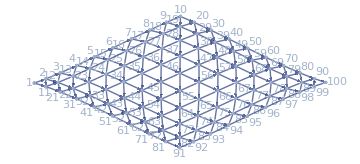

```mathematica
unpertHypergraph=tileTriHGraph[10,10];
[unpertHypergraph,VertexLabels->Automatic,ImageSize->Medium]
```

The next step is to insert a nonplanar hypergraph as a perturbation which is intended to be analogous to inserting an elementary particle into the discrete spacetime mesh.

## III. Inserting K_5 into the the spacetime mesh

The first nonplanar graph we will insert into our spacetime mesh is K_5, which we can see displayed as a hypergraph below.

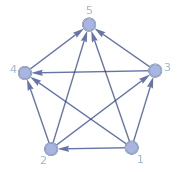

```mathematica
k5={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
[k5,VertexLabels->Automatic,ImageSize->Small]
```

We insert the K_5 hypergraph approximately into the center of the spacetime mesh.

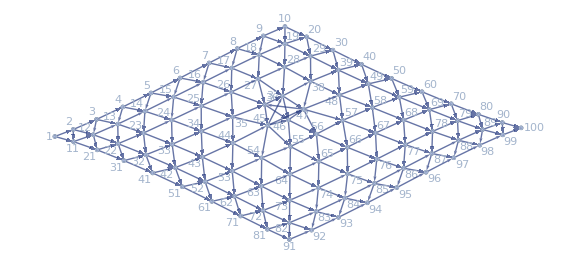

```mathematica
pertHypergraph=pertK5[unpertHypergraph];
[pertHypergraph,VertexLabels->Automatic,ImageSize->Large]
```

Now, we need to create the tools to generate the appropriate data to search for elementary particle behavior.

## IV. Create the tools to search for rules that generate elementary particle behavior

We want to find rules that result in localized changes in the evolution of perturbed hypergraphs. In the case of this project, the rules need to have the following specific properties: we want to be able to specify some range of vertices for which we can generate all of the rules that preserve the planarity, vertex number, and edge number of the associated connected graphs. Let us visualize, for example, all of the connected, planar graphs with 4 vertices and 4 edges in randomized directions below.

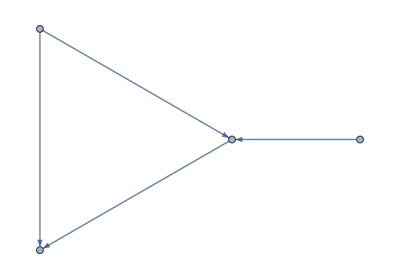
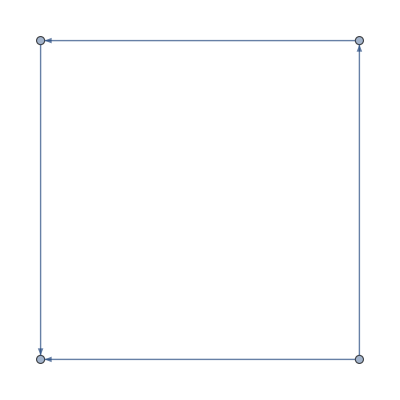

```mathematica
fourVtx4Edge=dirConnPlanarGraphs[4,4]
```

We convert these directed graphs into rules that can be recognized by the appropriate Wolfram Model resource function. We can demonstrate this below for the first directed graph in the list above.

```mathematica
fmtdFourVtx4Edge=fmtDirGraph[fourVtx4Edge[[1]]]
```

{{1,2},{1,3},{3,2},{4,3}}

We can now turn these formatted directed graphs into rules recognizable by the appropriate Wolfram Model resource function.

```mathematica
fourVtx4EdgeRules=genAllRules[4,4]
```

{{{{x,y},{x,z},{y,z},{z,w}}→{{y,x},{w,x},{z,y},{w,z}}},{{{y,x},{w,x},{z,y},{w,z}}→{{x,y},{x,z},{y,z},{z,w}}}}

We are interested in collecting the following data: the rule, a plot of the rule (to make it more human-readable), a plot that highlights in red the difference in the evolutions of the perturbed and unperturbed hypergraphs, a plot that highlights in blue the differences in their associated causal graphs (this might give us an analogy to the world line of our particle), and the number of steps of evolution of the unperturbed hypergraph (to see if the rule is associated with a quick termination). Let us see, for example, what this data looks like for the first rule we generated above after 10 steps of the evolution of our hypergraph.

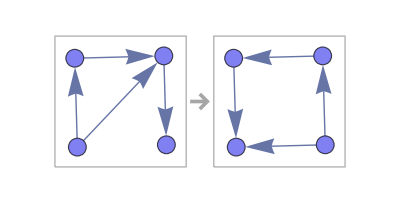
{{{{x,y},{x,z},{y,z},{z,w}}→{{y,x},{w,x},{z,y},{w,z}}},-Graphics-,-Graphics-,-Graphics-,11}

```mathematica
dataDemo=pertGraphData[fourVtx4EdgeRules[[1]],pertHypergraph,unpertHypergraph,10]
```

We will generate all of the permutations of the rules for any range of vertices and plug them into the appropriate Wolfram Model resource functions. We can see what this looks like for just 4 vertices below.

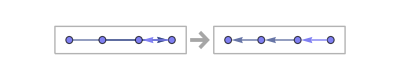
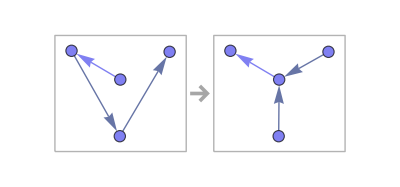
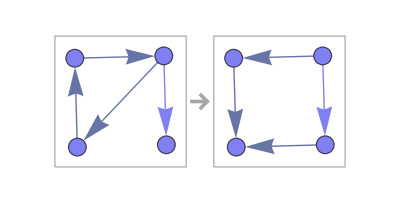
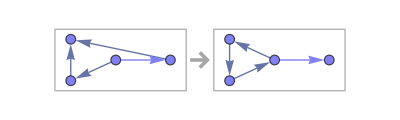
({{{x,w},{y,w},{w,z}}→{{y,x},{z,y},{w,z}}} | -Graphics-
{{{y,x},{z,y},{w,z}}→{{x,w},{y,w},{w,z}}} | -Graphics-
{{{x,y},{z,x},{y,z},{z,w}}→{{y,x},{w,x},{z,y},{z,w}}} | -Graphics-
{{{y,x},{w,x},{z,y},{z,w}}→{{x,y},{z,x},{y,z},{z,w}}} | -Graphics-)

```mathematica
rulesMat=planarityPrsvngRules[4,4]//MatrixForm
```

Let us demonstrate the generation of a dataset containing the data for all permutations of rules with 4 vertices for 10 steps of evolution and visualize the first two rows of the data.

```mathematica
ptclDataset=ptclEvolData[4,4,pertHypergraph,unpertHypergraph,10];
```

```mathematica
ptclDataset[[1;;2]]
```

Dataset[<>]

We can see that in these two cases, the changes caused by the perturbation have spread out throughout the entire mesh. We are instead looking for more localized changes. 

Now, we will use a high-level machine learning based clustering analysis method to see if we can cluster data by its index in the dataset. The results here are not of particular interest since this dataset is relatively small - but this example is meant to demonstrate the process that will be used later on the larger dataset. What we ultimately would like to see is the data split into three clusters - one where the evolution is trivial, one where the changes spread, and one where the changes remain localized.

```mathematica
assoc=AssociationThread[Range[Length[ptclDataset]]->Normal[ptclDataset[All,"finalStateHighlight"]]]
```

<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>

```mathematica
clus=FindClusters[assoc]
```

{{1},{2},{3},{4}}

Now that we have seen the data acquisition process, let us look for elementary particle behavior in rules that involve more vertices.

## V. Acquire and analyze the K_5 perturbation data

The first step to acquiring our data is to generate the spacetime mesh. The mesh here can be made to be rather large but due to time and computational cost constraints we will continue for now with a 10x10 vertex mesh.

```mathematica
unpertHypergraphLargeK5=tileTriHGraph[10,10];
```

Now we insert the perturbation K_5 into our mesh.

```mathematica
pertHypergraphLargeK5=pertK5[unpertHypergraphLargeK5];
```

Now we acquire the data and save it to a file. In this case, we search from 4 to 5 vertices for up to 10 steps of evolution.

```mathematica
ptclDatasetExpK5=ptclEvolData[4,5,pertHypergraphLargeK5,unpertHypergraphLargeK5,10];
```

```mathematica
Export["Desktop/ptclDatasetK5.wl",ptclDatasetExpK5];
```

Now let us look for clusters in the dataset.

```mathematica
ptclDatasetK5=Import["Desktop/ptclDatasetK5.wl"];
```

```mathematica
assocK5=AssociationThread[Range[Length[ptclDatasetK5]]->Normal[ptclDatasetK5[All,"finalStateHighlight"]]];
```

```mathematica
clusK5=FindClusters[assocK5];
```

The clustering analysis method clustered the hypergraphs into 26 groups: 1 cluster with 39 trivial evolutions and 25 separate clusters each containing one hypergraph that has a nontrvial evolution. There was an attempt to force the cluster into the 3 groups mentioned before but not enough data has been generated yet for a clustering analysis method to efficiently work. However, the framework for doing so is in place for future work that will generate larger sets of data. The rules with that generate the most interesting evolutions of our hypergraph can be seen below. The changes are localized, the causal graphs are mostly connected, and they did not terminate quickly. These may be good candidates for elementary particle behavior in the Wolfram Model. Tests on larger sets of data should be run to confirm these preliminary results.

```mathematica
ptclDatasetK5[[{3,19,20,21,26,49},All]]
```

Dataset[<>]

Now, let us repeat this procedure with the K_(3,3) perturbation.

## VI. Repeat the procedure for the K_(3,3) perturbation

We again start by generating our spacetime mesh.

```mathematica
unpertHypergraphLargeK33=tileTriHGraph[10,10];
```

Now let us add K_(3,3) (see below) to our spacetime mesh.

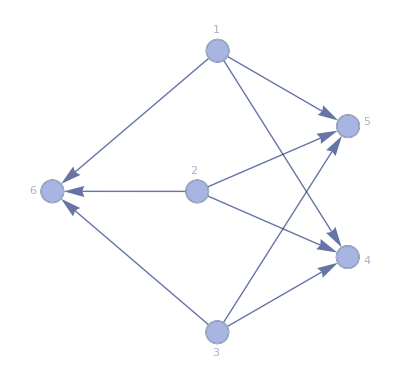

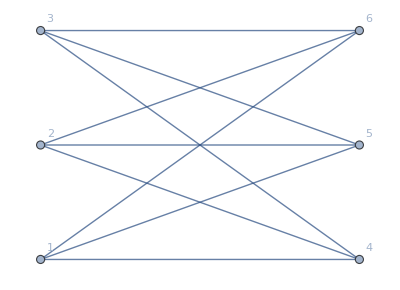

```mathematica
k33={{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}};
[k33,VertexLabels->Automatic,ImageSize->Tiny]
Graph[k33,GraphLayout->"MultipartiteEmbedding",VertexLabels->Automatic]
```

```mathematica
pertHypergraphLargeK33=pertK33[unpertHypergraphLargeK33];
```

Now we can collect the evolution data. Again, we will be looking at all permutations of the rules with 4 and 5 vertices for 10 steps of evolution and then saving the file.

```mathematica
ptclDatasetExpK33=ptclEvolData[4,5,pertHypergraphLargeK33,unpertHypergraphLargeK33,10];
```

```mathematica
Export["Desktop/ptclDatasetK33.wl",ptclDatasetExpK33];
```

Now we want to import the file and find clusters in the dataset.

```mathematica
ptclDatasetK33=Import["Desktop/ptclDatasetK33.wl"];
```

```mathematica
assocK33=AssociationThread[Range[Length[ptclDatasetK33]]->Normal[ptclDatasetK33[All,"finalStateHighlight"]]];
```

```mathematica
clusK33=FindClusters[assocK33];
```

The clustering analysis method produced a similar result to the last section. There were 20 clusters, one containing 45 trivial solutions and 19 individual clusters which contained each one single nontrivial solution. With more data in future trials the clustering analysis method should be more effective at sorting out the interesting evolutions. The most interesting rules for this perturbation of our hypergraph are shown below.

```mathematica
ptclDatasetK33[[{18,19,20},All]]
```

Dataset[<>]

None of the terminate quickly, they are all fairly localized, and the changes in their causal graphs seem to represent mostly connected world lines. The third rule in this dataset is particularly interesting because of its connected causal graph, but its changes in the hypergraph evolution appear to be slightly more spread out than we might hope to see. With more time and data this rule should be checked in the future for the persistence of this interesting behavior.

## Summary and Conclusions

In this project, we established an initial framework for searching for elementary particle behavior within the Wolfram Model. We started with a planar, triangularly tiled hypergraph, added a topological obstruction (a nonplanar structure - K_5 or K_(3,3)), and observed how the system evolved under the application of planarity-preserving rules. Several rules of interest were found in this preliminary test of the framework that showed behavior that might be analogous to the motion of an elementary particle moving through spacetime. 

	Many of the rules evolved trivially and terminated quickly. Finding elementary particle candidates in this way seems to be rare. One of the reason for this might be that we used a uniform spacetime mesh. A more diverse mesh might allow for more rules to evolve nontrivially and not terminate as quickly. A larger spacetime mesh should be used in addition to rules for hypergraphs with more vertices when time and computational cost is less of an issue. This could generate a larger dataset that would increase the effectiveness of the clustering analysis method in sifting through the less interesting evolutions. Different types of topological obstructions should be explored as well.
	
	The directions of the hypergraphs in the rules were randomized in this project notebook. In an initial test it seemed that the direction had a minimal effect on the evolution of the hypergraph, however it did have a measurable effect on the causal graphs. This effect should be incorporated into future investigations, especially for those interested in studying the world lines of elementary particles. Once a solid framework for generating a single elementary particle in spacetime has been established, multiple particles should be added into the system to search for analogies to quantum statistics and the dynamics of the quantum foam.

## Appendix: Initialization cells with user-defined functions

```mathematica
tileTriHGraph[rows_,cols_]:=
(* The function "tileTriHGraph" creates a triangular, tiled, planar hypergraph with an inputted number of rows and columns. *)
Module[{hypGraph,j,i},
hypGraph={};
(* "j" is the row and "i" is the vertex *)
For[j=1,j≤rows,j++,
(* conditions for each row before the last *)
If[j<rows,
For[i=1+cols*(j-1),i≤cols*j,i++,
(* condition for the first index of the jth row *)
If[i==1+cols*(j-1),
AppendTo[hypGraph,{i,i+1}];
AppendTo[hypGraph,{i,i+cols}]
];
(* condition for the middle indices of the jth row *)
If[i≠1+cols*(j-1)&&i≠cols*j,
AppendTo[hypGraph,{i,i+1}];
AppendTo[hypGraph,{i,i+(cols-1)}];
AppendTo[hypGraph,{i,i+cols}]
];
(* condition for the last index of the jth row *)
If[i==cols*j,
AppendTo[hypGraph,{i,i+(cols-1)}];
AppendTo[hypGraph,{i,i+cols}]
]
],
(* condition for the last row *)
For[i=1+cols*(j-1),i<cols*j,i++,
AppendTo[hypGraph,{i,i+1}]
];
];
];
Return[hypGraph]
]
```

```mathematica
pertK5[hypGraph_]:=
(* The function pertk5 adds the nonplanar graph Subscript[K, 5] as a perturbation to a planar, triangularly tiled hypergraph. 
NOTE: This function is built to to take as input a hypergraph generated by the user-defined function tileTriHGraph. *)
Module[{cols,rows,i,newHypGraph=hypGraph},
(* calculate the # of rows and columns of the inputted hypergraph *)
cols=newHypGraph[[2,2]]-1;
rows=Max[newHypGraph]/cols;
(* calculate the index of the vertex "i" in the middle of the hypergraph of which to add three edges to insert Subscript[K, 5] *)
If[OddQ[rows]==True,
i=Floor[Max[newHypGraph]/2],
i=Floor[(Max[newHypGraph]-cols)/2];
];
AppendTo[newHypGraph,{i,i+2}];
AppendTo[newHypGraph,{i,i-cols+2}];
AppendTo[newHypGraph,{i+2,i-cols+1}];
Return[newHypGraph]
]
```

```mathematica
pertK33[hypGraph_]:=
(* The function pertk33 adds the nonplanar graph Subscript[K, 3,3] to a planar, triangularly tiled hypergraph created by the function tileTriHGraph. *)
Module[{cols,rows,i,newHypGraph=hypGraph},
(* calculate the # of rows and columns in the inputted hypergraph *)
cols=newHypGraph[[2,2]]-1;
rows=Max[newHypGraph]/cols;
(* calculate the index of the vertex "i" in the middle of the hypergraph of which to add three edges to create Subscript[K, 5]*)
If[OddQ[rows]==True,
i=Floor[Max[newHypGraph]/2],
i=Floor[(Max[newHypGraph]-cols)/2];
];
AppendTo[newHypGraph,{i,i-cols+2}];
AppendTo[newHypGraph,{i+1,i-cols}];
AppendTo[newHypGraph,{i+2,i-cols}];
AppendTo[newHypGraph,{i+2,i-cols+1}];
Return[newHypGraph]
]
```

```mathematica
dirConnPlanarGraphs[vtx_,edge_]:=
(* The function dirConnPlanarGraphs returns a list of all of the connected, planar graphs with the inputted number of vertices (vtx) and edges (edge) in randomized directions.
NOTE: The directions are randomized because I was mostly interested in the evolution of the hypergraph which seemed trivially affected by the directions, but the causal graphs seemed to be nontrivially affected by the directions so this function may want to be edited to include all permutations of directions in the future when searching for world lines in causal graphs *)
DirectedGraph[#,"Random"]&/@Select[GraphData/@GraphData["Planar",vtx],ConnectedGraphQ[#]==True&&EdgeCount[#]==edge&]
```

```mathematica
fmtDirGraph[dirGraph_]:=
(* The function fmtDirGraph takes a directed graph as input and returns a formatted list that can be the left or right-hand-side of a Wolfram Model rule. *)
Module[
{i,fmtdList},
fmtdList={};
For[i=1,i≤Length[EdgeList[dirGraph]],i++,
AppendTo[fmtdList,{EdgeList[dirGraph][[i,1]],EdgeList[dirGraph][[i,2]]}]
];
Return[fmtdList]
]
```

```mathematica
genAllRules[vtx_,edge_]:=
(* The function genAllRules returns a list of all of the possible rules (directed graph -> directed graph) for permutations of randomly directed, connected, planar graphs with an inputted number of vertices (vtx) and edges (edge). 
NOTE: This function depends on the user-defined functions dirConnPlanarGraphs and fmtDirGraph. *)
Module[
{perm,i,rule},
rule={};
perm=Permutations[dirConnPlanarGraphs[vtx,edge],{2}];
For[i=1,i≤Length[perm],i++,
AppendTo[rule,
{fmtDirGraph[perm[[i,1]]]->fmtDirGraph[perm[[i,2]]]}];
];
Return[/@rule]
]
```

```mathematica
pertGraphData[rule_,pertInit_,unpertInit_,evolSteps_]:=
(* The function pertGraphData takes as input a rule, perturbed and unperturbed hypergraphs, and the number of steps desired in the evolution. It returns a list containing the rule, a plot of the rule, a plot highlighting the difference between the perturbed and unperturbed final state graphs, a plot highlighting the difference between their respective causal graphs, and the number of evolution states of the unperturbed hypergraph. *)
Module[
{pertEvolObj,unpertEvolObj,data,causalGraphDiff},
pertEvolObj=[rule,pertInit,evolSteps];
unpertEvolObj=[rule,unpertInit,evolSteps];
causalGraphDiff=GraphDifference[unpertEvolObj["CausalGraph"],pertEvolObj["CausalGraph"]];
data={
rule,
RulePlot[[rule]],
(* finds the difference between the last evolution step of the perturbed and unperturbed hypergraphs, the perturbed evolution object is truncated in an effort to maintain an equal length between both states lists *)
Last[MapThread[[#,EdgeStyle-><|Alternatives@@#2->Directive[Thick,Red]|>,ImageSize->120]&,{unpertEvolObj["StatesList"],MapThread[Complement,{unpertEvolObj["StatesList"],pertEvolObj["StatesList"][[1;;Length[unpertEvolObj["StatesList"]]]]}]}]],
HighlightGraph[unpertEvolObj["CausalGraph"],Style[causalGraphDiff,Blue,Thickness[0.01]]],Length[unpertEvolObj["StatesList"]]};
Return[data]
]
```

```mathematica
planarityPrsvngRules[minVtx_,maxVtx_]:=
(* The function planarityPrsvngRules generates a list of all of the Wolfram Model rules that preserve planarity for a minimum and maximum number of vertices. 
NOTE: This function depends on the user-defined function genAllRules *)
Module[
{i,j,ruleForm,rulePlots,k,rulesList},
rulesList={};
For[i=minVtx,i≤maxVtx,i++,
(* starts looking for rules with iteration vertex - 1 edges and keeps looking for rules with increasingly more edges until it reaches its first edge number that does not have any associated planarity preserving rules *)
j=i-1;
While[genAllRules[i,j]≠{},
ruleForm=genAllRules[i,j];
rulePlots=RulePlot/@/@ruleForm;
For[k=1,k≤Length[ruleForm],k++,
rulesList=AppendTo[rulesList,{ruleForm[[k]],rulePlots[[k]]}]
];
j=j+1
]
];
Return[rulesList]
]
```

```mathematica
ptclEvolData[minVtx_,maxVtx_,pertInit_,unpertInit_,evolSteps_]:=
(* The function ptclEvolData returns a dataset containing the data collected for all of the rules collected for a range of vertices.
NOTE: This function depends on the user-defined functions planarityPrsvngRules and pertGraphData. *)
Module[
{rules,data,dataAssoc,i},
dataAssoc={};
rules=planarityPrsvngRules[minVtx,maxVtx];
For[i=1,i≤Length[rules[[All,1]]],i++,
data=pertGraphData[rules[[i,1]],pertInit,unpertInit,evolSteps];
AppendTo[dataAssoc,<|"rule"->data[[1]],"rulePlot"->data[[2]],"finalStateHighlight"->data[[3]],"causalGraphHighlight"->data[[4]],"states"->data[[5]]|>]
];
Return[Dataset[dataAssoc]]
]
```

## Keywords

Wolfram Model

Topological Obstruction

Machine Learning

Clustering Analysis

## Acknowledgement

I would like to extend my sincerest gratitude to my mentor Mano who made herself constantly available to talk about my project and help me work through my ideas. I would also like to acknowledge Xerxes, Jonathan, and Dr. Stephen Wolfram for helping me focus the direction I went with this project. I would also like to thank Erin and Danielle for all of their help making the Wolfram Physics Winter School 2021 a fun and rewarding experience. Finally, I would like to thank all of the other students in my cohort for the fascinating discussions and teaching me more about my favorite thing in the world - physics!

## References

[1] Wolfram, Stephen. “A Class of Models with the Potential to Represent Fundamental Physics.” Complex Systems 29.2 (2020): 107–536. Crossref. Web.